```mathematica
1)  Derive a holonomic system for the internal triple integral of the expection of an Euler characteristic number
```

```mathematica
<< RISC`HolonomicFunctions` (* the pacakge is available in http://www.risc.jku.at/research/combinat/software/ergosum/installation.html#download *)
```

HolonomicFunctions Package version 1.7.3 (21-Mar-2017)
written by Christoph Koutschan
Copyright Research Institute for Symbolic Computation (RISC),
Johannes Kepler University, Linz, Austria

--> Type  ?HolonomicFunctions  for help.

```mathematica
stheta=(2 s)/(1+s^2); (* make a universal transformation for Sin[theta] *)
```

```mathematica
ctheta=(1-s^2)/(1+s^2); (* make a universal transformation for Cos[theta] *)
```

```mathematica
sphi=(2 t)/(1+t^2); (* make a universal transformation for Sin[phi] *)
```

```mathematica
cphi=(1-t^2)/(1+t^2);(* make a universal transformation for Cos[phi] *)
```

```mathematica
R=s1 (b sphi stheta+d cphi ctheta-m11)^2+s2 (-b sphi ctheta+d cphi stheta-m21)^2+s2 (b cphi ctheta+d sphi stheta-m22)^2+s1 (-b cphi stheta+d sphi ctheta)^2; (* input R in the integrand *)
```

```mathematica
f=2/(1+t^2 )2/(1+s^2) (d^2-b^2) (s1 s2)/(2 Pi)^2 Exp[-1/2 R]; (*input the integrand of Example 1 *)
```

```mathematica
f1=Simplify[f/.{s1->2,s2->1,m11->1,m21->-1,m22->1}] ;(* specify the parameters as that in Example 1*)
```

```mathematica
ann=Annihilator[f1,{Der[d],Der[b],Der[s],Der[t]}];(* compute the differential equations ann of f1 *)
```

```mathematica
Timing[ann1=CreativeTelescoping[ann,Der[t]][[1]];] (* compute the differential equations ann1 of the inner single integral *)
```

{0.743612,Null}

```mathematica
supp1 = {1, Der[b], Der[d], Der[b]^2, Der[b] Der[d], Der[d]^2, Der[d]^3} (* a support set for a differential equation of the inner double integral *)
```

{1,Der[b],Der[d],Der[b]^2,Der[b] Der[d],Der[d]^2,Der[d]^3}

```mathematica
Timing[op1=FindCreativeTelescoping[ann1,Der[s], Support -> supp1][[1,1]];] (* compute a differential equation op1 of the inner double integral with support in supp1 *)
```

{1.9834,Null}

```mathematica
supp2 = {1, Der[b], Der[d], Der[b]^2, Der[b] Der[d], Der[d]^2, Der[b]^3, Der[b]^2 Der[d], Der[b] Der[d]^2, Der[d]^3};(* another support set for another differential equation of the inner double integral *)
```

```mathematica
Timing[op2=FindCreativeTelescoping[ann1,Der[s], Support -> supp2][[1,1]];](* compute another differential equation op2 of the inner double integral with support in supp2 *)
```

{38.4391,Null}

```mathematica
Timing[ann2 = OreGroebnerBasis[{op1, op2}];] (* compute a holonomic system ann2 of the inner double integral *)
```

{0.262255,Null}

```mathematica
UnderTheStaircase[ann2] (* ann2 has holonomic rank 6 *)
```

{1,D_b,D_d,D_b^2,D_d D_b,D_b^3}

```mathematica
supp3 = Table[ Der[d]^i,{i, 0, 10}] (* a support set for a differential equation of the inner triple integral *)
```

{1,Der[d],Der[d]^2,Der[d]^3,Der[d]^4,Der[d]^5,Der[d]^6,Der[d]^7,Der[d]^8,Der[d]^9,Der[d]^10}

```mathematica
Timing[ann3=FindCreativeTelescoping[ann2,Der[b], Support -> supp3][[1,1]];] (* compute a holonomic system ann3 of the inner triple integral with support in supp3 *)
```

{180.641,Null}

```mathematica
2)  Use HGM and NIntegrate to compute the 4-fold  integral of the expection of an Euler characteristic number
```

```mathematica
LeadingCoefficient[ann3] // Factor (* this is the leading coefficient of ann3, it has factor d^3 and will cause problem when we do numerical solving of the differential equation ann3 around point d = 0 *)
```

-2 d^3 (631817657118720+2095657034925312 d^2+724467464883216 d^4+629948574520272 d^6-2294085002746464 d^8-2049365542469976 d^10-535637217809988 d^12+434768339332692 d^14+233259167958732 d^16-49281849447462 d^18-9631943312778 d^20+1257059674746 d^22+183170190204 d^24-190350884835 d^26+13959917376 d^28+2249744448 d^30-15340576 d^32-30430080 d^34+1296000 d^36)

```mathematica
ann4 = DFinitePlus[{ann3}, ToOrePolynomial[{Sum[RandomInteger[{1, 1000}] Der[d]^i, {i, 0, 3}]}, OreAlgebra[Der[d]]]][[1]]; (* Using desingularization technique to remove the factor d^3 in ann3 *)
```

```mathematica
LeadingCoefficient[ann4] // Factor (* we can reduce the multiplicity of d in ann3, but d is non-removable *)
```

250 d (45635784490000328111141898806732765532970439147520000-263828960452276828355054950847552689860431789433815040 d+243087146756788261804315657136464248477853512231813120 d^2+2158925017235485005486046911988537583870846890489282560 d^3-10354902216867700978617089003435964962046653420167495680 d^4+23805301402251879416494690829598034398476210023411138560 d^5-34047089992156822516112544532941081371616749805359235072 d^6+28890871220792745488882481521155819000123081779530588160 d^7-9464186692200575126873442142654876389110643950792343552 d^8-1514812922193802730436215108291833262402444222612613120 d^9-7350971527911951151479524353310084884518311384581724160 d^10+11788650131933884618171514881020887515911164689049333760 d^11+24247000303017743095643417840179242750120101033582489088 d^12-107045873348131991237485157516669444683838253906501093120 d^13+204073493840804622841719340631581906703187820974976937472 d^14-276981446129752718241357425564757992022512880117126524928 d^15+305385791147704289518411857530784229736408102767922033856 d^16-298489808217796851669356422271421602740837803053576042496 d^17+284917503917890289009721253000403405563340589324158346432 d^18-278631181185270124229886351212648002213251477362167457664 d^19+266755650684150771859361066266793916140489065574004956928 d^20-233665371392267406907504496761241484514470424717014758592 d^21+184692257251835894205387022294728203553321703211817979680 d^22-139913645630872564312730037233151021365061387322541217024 d^23+110790706704660371737984725817507698050285377654664612880 d^24-92577301045662029340102576260599246271564592322262179776 d^25+76181392865348171580502823988615192320469634550427831504 d^26-57632774109866219475886720062126421608352503035602333344 d^27+37592990283677822873377143623368079595541841255159180880 d^28-18602195713944536212228336797836035964047726380358583040 d^29+3659203144033876055176243304339885512787913077060990568 d^30+5461069613955074016423482684999852599772825152799711136 d^31-9010563914554329049157041104513308990810014284935177224 d^32+8619262464207601052520667073896999410248120740408256640 d^33-6358522674482927409380612016514495133973989500725242160 d^34+3872469229150030719402597239107481351106459809915059408 d^35-1940385055176445391523591642065413478377572624334351048 d^36+697486295400373637179444423993465008212641691495772048 d^37-29329885131194094848436982512190835615346108600820268 d^38-227800433264311252871220597499759099182414146017525776 d^39+240792757377590614175189129723463724548171886306410932 d^40-157374855760606035126360769285640811113024510652225920 d^41+73117460553146866610451923743321732670135655679216860 d^42-22530635417017575873080520142698432848197325931065856 d^43+1918679582497442781129197219368359176618178239392960 d^44+2911063799175989726184711658006575691307518560370224 d^45-2399818346555451623027500222059947415529085398241994 d^46+1163931813168483956331330068176728778153495650228368 d^47-398983482173893730832715467335827636830885944844078 d^48+82436875101251359277525628822840489579212203713952 d^49+6838820096206155856178027914854228897036417446292 d^50-14797157063258052181324157871741453608067594327824 d^51+5762109914175080399384809193369558311446673077280 d^52+301824022916198823133751781350596337161983495920 d^53-1653794042892601930162229990674268734539888263115 d^54+1045236028437313483746546383178377727929051014816 d^55-368218554301065031553779072284566691876182839404 d^56+66713660983736885749329549155060364605555150400 d^57+6092382893201059060432400815920766582510142580 d^58-9738070014314752037086982205638056550041497600 d^59+4608257025248532208462102807583317462519968000 d^60-1573117512093543003002024901367249218631680000 d^61+361728091860497382317861789346859589680200000 d^62-14518740408405345662609133056519251200000000 d^63-27899524676361776931741125878162650000000000 d^64+12098710880309047918551664682475000000000000 d^65-2374659253465686432253294516406250000000000 d^66+105437956830539375995966406250000000000000 d^67+65290355486969688385675048828125000000000 d^68-18545801832782440136718750000000000000000 d^69+2442140762220366668701171875000000000000 d^70-170822406637573242187500000000000000000 d^71+5131569027900695800781250000000000000 d^72)

```mathematica
uts3 = UnderTheStaircase[{ann3}] (* the parametric derivatives under the stair of ann3 *)
```

{1,D_d,D_d^2,D_d^3,D_d^4,D_d^5,D_d^6,D_d^7,D_d^8,D_d^9}

```mathematica
Timing[inits = NIntegrate[Together[ApplyOreOperator[uts3,1/2 f1] /. {d -> 1/2}], {b, -Infinity, Infinity}, {s, -Infinity, Infinity}, {t, -Infinity, Infinity},MaxRecursion->20,Method->{GlobalAdaptive,MaxErrorIncreases->10000}];] (* compute the initial value for the Pfaffian system of ann3 at d = 1/2. Since ann3 has a singularity at d = 0, it is not suitable to choose the initial point at d = 0 *)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.629452 and 0.0000229486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{1103.31,Null}

```mathematica
eqnsd = ApplyOreOperator[ann3, y[d]] == 0; (* set up the differential equation for the inner triple integral *)
```

```mathematica
inits1 = Table[D[y[d], {d, i}] == inits[[i +1 ]], {i, 0, 9}] /. {d -> 1/2} (* set up the initial values for eqnsd at d = 1/2 *)
```

{y[1/2]==-0.798885,y'[1/2]==0.683103,y''[1/2]==1.32947,y^(3)[1/2]==-0.629452,y^(4)[1/2]==-4.73677,y^(5)[1/2]==-12.9357,y^(6)[1/2]==42.4342,y^(7)[1/2]==267.695,y^(8)[1/2]==-680.996,y^(9)[1/2]==-4656.36}

```mathematica
s1 = NDSolve[Join[{eqnsd},inits1], y, {d, 1/2, 30}]; (* numerical solving of the diffential equation eqnsd from 1/2 to 30 *)
```

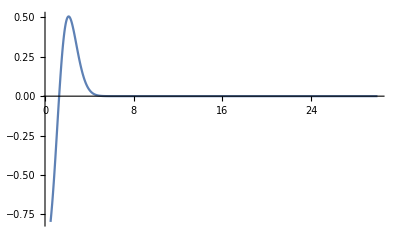

```mathematica
Plot[Evaluate[y[d]/.s1],{d,1/2,30},PlotRange->All] (* y[d] is very small when d ≥ 5*)
```

```mathematica
HGM1 = Table[NIntegrate[y[d] /. s1, {d, i, 30}][[1]], {i, 1, 6}] (* Using numerical integration to compute the integral in Example1 for x from 1 to 6. The results are as accurate as that in Prof. Kuriki's mathematica notebook*)
```

{0.745835,0.567729,0.144879,0.0146728,0.000582526,8.79942×10^-6}

```mathematica
3)  Use HGM directly to compute the 4-fold  integral  of the expection of an Euler characteristic number
```

```mathematica
ann4 = OreTimes[ann3, Der[d]] /. {d -> x} // Factor;(* ann4 is the annihilator for the 4-fold integral F[x] in Example1 *)
```

```mathematica
uts = UnderTheStaircase[{ann4}] (* the parametric derivatives of ann4 *)
```

{1,D_x,D_x^2,D_x^3,D_x^4,D_x^5,D_x^6,D_x^7,D_x^8,D_x^9,D_x^10}

```mathematica
Timing[init1 = NIntegrate[1/2 f1 , {d , 1/2, Infinity},{b, -Infinity, Infinity}, {s, -Infinity, Infinity}, {t, -Infinity, Infinity},MaxRecursion->20,Method->{GlobalAdaptive,MaxErrorIncreases->10000}];] (* compute the inital value F[1/2] *)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.456409 and 0.0000154335 for the integral and error estimates.

{41.9077,Null}

```mathematica
inits = Prepend[-inits, init1] (* the initial points F^(k)[1/2], k = 0, .., 10 *)
```

{0.456409,0.798885,-0.683103,-1.32947,0.629452,4.73677,12.9357,-42.4342,-267.695,680.996,4656.36}

```mathematica
eqnsd = ApplyOreOperator[ann4, y[x]] == 0; (* set up the differential equation for the 4-fold integral in Example1 *)
```

```mathematica
inits1 = Table[D[y[x], {x, i}] == inits[[i +1 ]], {i, 0, 10}] /. {x -> 1/2} (* set up the initial values for eqnsd at d = 1/2 *)
```

{y[1/2]==0.456409,y'[1/2]==0.798885,y''[1/2]==-0.683103,y^(3)[1/2]==-1.32947,y^(4)[1/2]==0.629452,y^(5)[1/2]==4.73677,y^(6)[1/2]==12.9357,y^(7)[1/2]==-42.4342,y^(8)[1/2]==-267.695,y^(9)[1/2]==680.996,y^(10)[1/2]==4656.36}

```mathematica
s2 = NDSolve[Join[{eqnsd},inits1], y, {x, 1/2, 30}] (* numerical solving of the diffential equation eqnsd from 1/2 to 30 *)
```

{{y→InterpolatingFunction[{{0.5, 30.}}, <>]}}

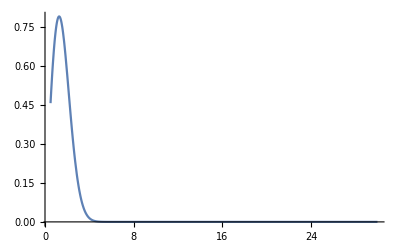

```mathematica
Plot[Evaluate[y[x]/.s2],{x,1/2,30},PlotRange->All] (* y[x] is very small when x ≥ 5*)
```

```mathematica
HGM2 = Table[(y[x] /. s2)[[1]], {x, 1, 6}](* The results are as accurate as that in Prof. Kuriki's mathematica notebook*)
```

{0.745833,0.567727,0.144877,0.0146714,0.000581059,7.33124×10^-6}

```mathematica
4) Monte Carlo study for the Expectation of Euler charateristic number in Example 1
```

```mathematica
EulerChar[A_,x_]:=Module[{b,d,a,c},{b,d}=SingularValueList[A];(*b and d are singular value of A*)If[TrueQ[b≥x],a=Sign[b^2-d^2],a=0];
If[TrueQ[d≥x],c=Sign[d^2-b^2],c=0];
Return[a+c];]; (* compute the Euler charateristic number of a random matrix A w.r.t. x*)
```

```mathematica
Clear[s1, s2];
```

```mathematica
sub={s1->2,s2->1,m11->1,m21->-1,m22->1}
```

{s1→2,s2→1,m11→1,m21→-1,m22→1}

```mathematica
S=DiagonalMatrix[{1/Sqrt[s1],1/Sqrt[s2]}]/.sub
```

{{1/(√2),0},{0,1}}

```mathematica
M={{m11,0},{m21,m22}}/.sub
```

{{1,0},{-1,1}}

```mathematica
n =10000000 (* the number of iterations *)
```

10000000

```mathematica
ra=Table[S.{RandomVariate[NormalDistribution[],2,WorkingPrecision->10],RandomVariate[NormalDistribution[],2,WorkingPrecision->10]}+M,{i,1,n}]; (* generate n random matrix A*)
```

```mathematica
Timing[mc = Table[ N[Sum[EulerChar[ra[[i]],x],{i,1,n}]/n], {x, 1, 6}];] (*the results of expectation of Euler characteristic number by Monte Carlo study *)
```

{2838.39,Null}

```mathematica
mc (* The results are as accurate as that in Prof. Kuriki's mathematica notebook *)
```

{0.745977,0.567624,0.14491,0.0146791,0.0005798,9.×10^-6}